```mathematica
ClearAll[files, importfile, raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/3.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/~$3.xlsx}

```mathematica
importfile = files⟦4⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/331/3.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"B"->(Around[#B,#dB]&),"I"->(Around[#I,#dI]&)|>]
```

Dataset[<>]

## Dataset2

```mathematica
dataset2=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"B"->(Around[#B,#dB]&),"I"->(Around[#I,#dI]&)|>]
```

Dataset[<>]

## Dataset3

```mathematica
dataset3=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset3WithErrs=dataset3[All,<|"B"->(Around[#B,#dB]&),"I"->(Around[#I,#dI]&)|>]
```

Dataset[<>]

## Dataset4

```mathematica
dataset4=makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
dataset4WithErrs=dataset4[All,<|"B"->(Around[#B,#dB]&),"I"->(Around[#I,#dI]&)|>]
```

Dataset[<>]

## Dataset5

```mathematica
dataset5=makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
dataset5WithErrs=dataset5[All,<|"B"->(Around[#B,#dB]&),"I"->(Around[#I,#dI]&)|>]
```

Dataset[<>]

```mathematica
ClearAll[x,y]
```

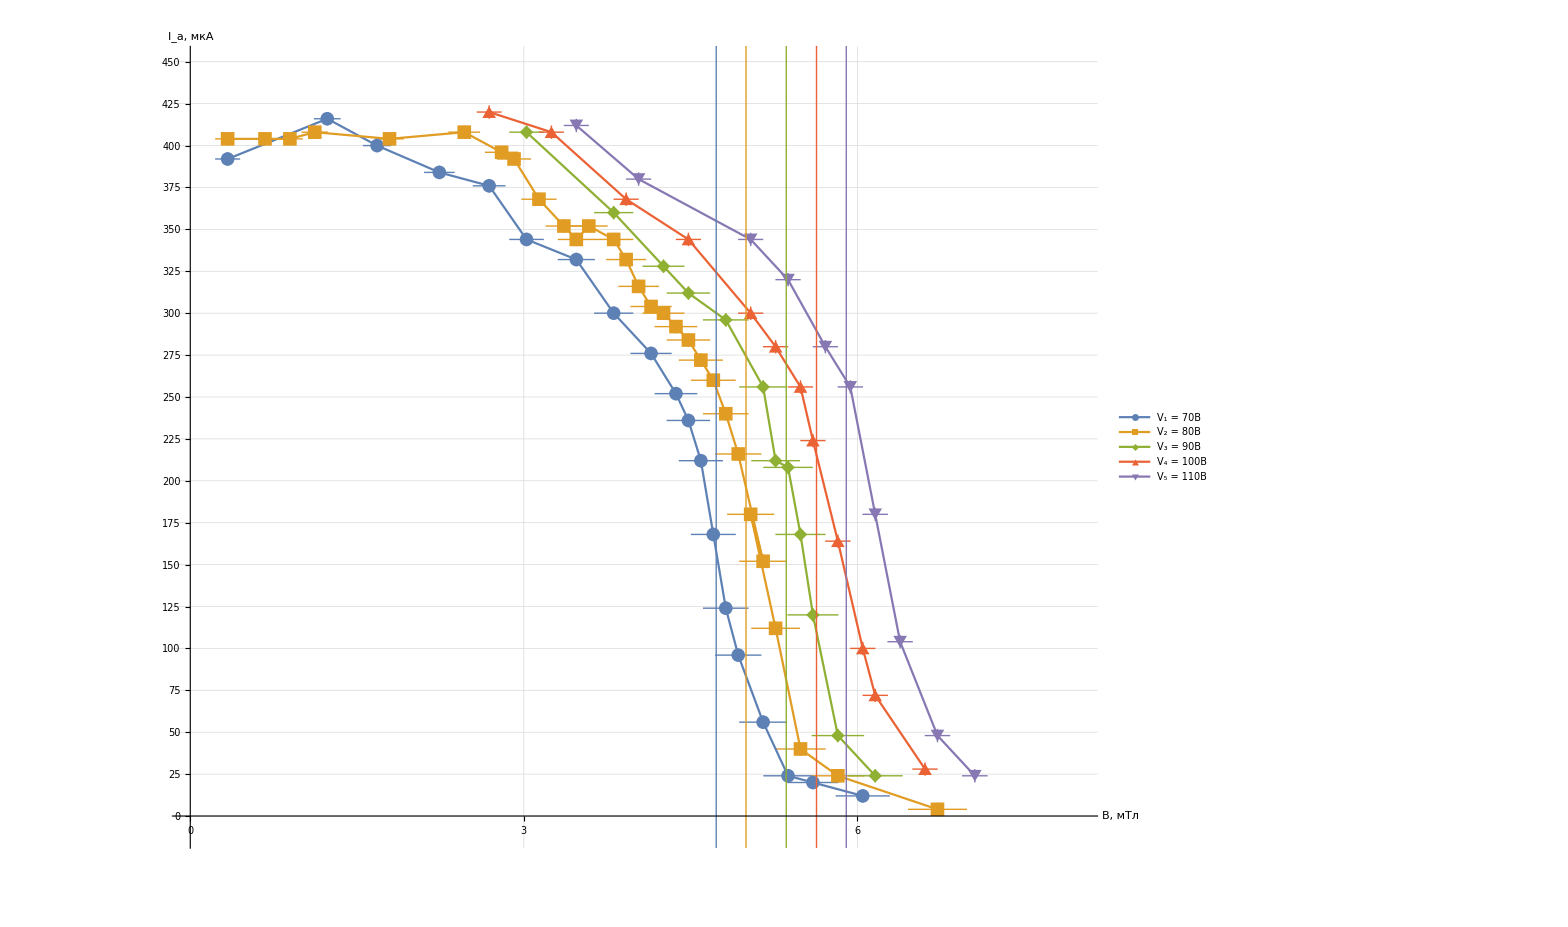

```mathematica
Show[
ListPlot[{dataset1WithErrs,dataset2WithErrs,dataset3WithErrs,dataset4WithErrs,dataset5WithErrs},
AxesLabel->{Style["B, мТл",Large],Style["I_(:0430), мкА",Large]},
AxesStyle->Directive[Arrowheads[{0.02}],Black], 
ImageSize->1500,
GridLines->{Range[0,430,0.125.00], Range[0,500,12.5]},
Ticks-> {Range[0,420,1],Range[0,500,25]}, 
TicksStyle->20,
Joined->True,
(*InterpolationOrder->4,*)
(*PlotStyle->Thickness[0.001]*)
PlotRange->{{0,8},{-10,450}},
PlotMarkers->{Automatic,14},
PlotLegends->Placed[LineLegend[
Automatic,
{"V_1 = 70B","V_2 = 80B","V_3 = 90B","V_4 = 100B","V_5 = 110B"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.2],Scaled[0.4]}
]
],
Graphics[{{RGBColor["#5f82b5"],Thick,Line[{{4.73,-100},{4.73,1000}}]}, (* 9 точек, начиная с -3 *)
{RGBColor["#e09c24"],Thick, Line[{{4.998,-100},{4.998.00,1000}}]}, (* 8 точек, начиная с -3  *)
{RGBColor["#8fb031"],Thick, Line[{{5.36,-100},{5.36.00,1000}}]}, (* 7 точек, начиная с -2 *)
{RGBColor["#ec6235"],Thick, Line[{{5.632,-100},{5.632.00,1000}}]}, (* .007 точке, начиная с -2 *)
{RGBColor["#8778b2"],Thick, Line[{{5.9,-100},{5.9,1000}}]}}] (* 7 точке, начиная с -2 *)
]
```

```mathematica
Color
```